```mathematica
(*---CORE FUNCTION---*)
ClearAll[simulateZombieSystem];

simulateZombieSystem[params_Association]:=
Module[
{beta=params["beta"],
gamma=params["gamma"],
a=params["a"],
b=params["b"],
c=params["c"],
d=params["d"],
interactionRate=params["interactionRate"],
kBeta=params["kBeta"],
kGamma=params["kGamma"],
Aβ=params["Aβ"],
Aa=params["Aa"],
Tseason=params["Tseason"],
phi=params["phi"],
w1=1,
w2=1.2,
w3=0.8,
betaSeasonal,
aSeasonal,
betaEff,
gammaEff,
equations,
solution
},

(*Seasonal effects*)
betaSeasonal[t_]:=beta*(1+Aβ*Sin[2*Pi*t/Tseason]);
aSeasonal[t_]:=a*(1+Aa*Sin[2*Pi*t/Tseason+phi]);

(*Coupling effects*)
betaEff[t_]:=betaSeasonal[t]/(1+kBeta*prey[t]);
gammaEff[t_]:=gamma*(1+kGamma*predator[t]/(1+predator[t]));
(*ODE system*)

equations={
S'[t]==-betaEff[t] S[t] (w1 Z1[t]+w2 Z2[t]+w3 Z3[t]),
Z1'[t]==betaEff[t] w1 S[t] Z1[t]-gammaEff[t] Z1[t],
Z2'[t]==betaEff[t] w2 S[t] Z2[t]-gammaEff[t] Z2[t],
Z3'[t]==betaEff[t] w3 S[t] Z3[t]-gammaEff[t] Z3[t],
R'[t]==gammaEff[t] (Z1[t]+Z2[t]+Z3[t]),
prey'[t]==aSeasonal[t] prey[t]-b prey[t] predator[t]-interactionRate (Z1[t]+Z2[t]+Z3[t]) prey[t],
predator'[t]==c prey[t] predator[t]-d predator[t],

(*Initial conditions*)
S[0]==0.99,
Z1[0]==0.005,
Z2[0]==0.003,
Z3[0]==0.002,
R[0]==0,
prey[0]==0.99,
predator[0]==0.01

};
(*Solve system*)

solution=NDSolve[
equations,
{S,Z1,Z2,Z3,R,prey,predator},
{t,0,100},
Method->"StiffnessSwitching"
];
(*Return rules so caller can extract functions*)
First[solution]];

(*---TEST PARAMETERS---*)
params=<|"beta"->0.3,"gamma"->0.1,"a"->0.1,"b"->0.02,"c"->0.05,"d"->0.05,"interactionRate"->0.01,"kBeta"->0.3,"kGamma"->0.5,"Aβ"->0.3,"Aa"->0.2,"Tseason"->50,"phi"->0|>;

(*---RUN CORE SYSTEM---*)
solRules=simulateZombieSystem[params];

(*Extract functions from rules*)
Sfun=S/. solRules;
Z1fun=Z1/. solRules;
Z2fun=Z2/. solRules;
Z3fun=Z3/. solRules;
Rfun=R/. solRules;
preyFun=prey/. solRules;
predFun=predator/. solRules;

ZtotalFun[t_]:=Z1fun[t]+Z2fun[t]+Z3fun[t];
```

## Limit Cycle Tests

## Observation-based tests with single parameter sets

### Time Series Inspection

```mathematica
ClearAll[plotZombieTimeSeries];

plotZombieTimeSeries[params_Association,tmax_:200]:=
Module[
{solRules,Sfun,Z1fun,Z2fun,Z3fun,Rfun,preyFun,predFun,ZtotalFun,t},
solRules=simulateZombieSystem[params];

If[!ListQ[solRules],
Return["Simulation failed"]];

(*Extract solution functions*)
Sfun=S/. solRules;
Z1fun=Z1/. solRules;
Z2fun=Z2/. solRules;
Z3fun=Z3/. solRules;
Rfun=R/. solRules;
preyFun=prey/. solRules;
predFun=predator/. solRules;
ZtotalFun[t_]:=Z1fun[t]+Z2fun[t]+Z3fun[t];

(*Plot Ztotal,prey,predator over time*)
Plot[
{ZtotalFun[t],
preyFun[t],
predFun[t]},
{t,0,tmax},
PlotLegends->{"Ztotal","Prey","Predator"},
PlotStyle->{Red,Green,Blue},
Frame->True,
FrameLabel->{"Time","Population"},
PlotRange->All
]
]
```

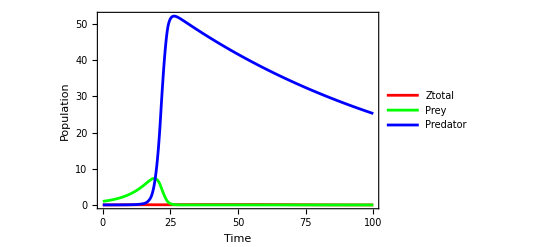

```mathematica
Print[plotZombieTimeSeries[params,100]]
```

### Phase portraits

```mathematica
(*---A2:Phase Portrait for Prey vs Predator---*)
ClearAll[plotZombiePhasePortrait];

plotZombiePhasePortrait[params_Association,{preyRange_,predatorRange_},gridStep_:0.5]:=
Module[
{a,b,c,d,interactionRate,Tseason,Aa,phi,t=0,preyDeriv,predatorDeriv,vectorField},

(*Extract parameters*)
a=params["a"];
b=params["b"];
c=params["c"];
d=params["d"];
interactionRate=params["interactionRate"];
Aa=params["Aa"];
Tseason=params["Tseason"];
phi=params["phi"];

(*Define seasonal prey growth*)aSeasonal=a*(1+Aa*Sin[2 Pi t/Tseason+phi]);
(*Derivatives at fixed t*)preyDeriv[p_,q_]:=aSeasonal*p-b*p*q-interactionRate*p*0.01;
(*assume fixed Ztotal~0.01*)predatorDeriv[p_,q_]:=c*p*q-d*q;

(*Create vector field*)
vectorField=VectorPlot[
{preyDeriv[x,y],predatorDeriv[x,y]},
{x,preyRange[[1]],preyRange[[2]]},{y,predatorRange[[1]],predatorRange[[2]]},
AxesLabel->{"Prey","Predator"},
VectorScale->Small,
StreamPoints->Fine,
PlotLabel->"Phase Portrait: Prey vs Predator"
];

vectorField
]

(*Example usage*)
plotZombiePhasePortrait[params,{{0,1},{0,1}}]
```

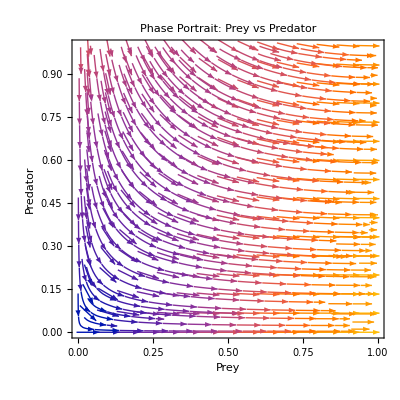

### Poincare Sections

```mathematica
ClearAll[plotPoincareSection];

params["beta"]=0.2;
params["a"]=0.05;
params["interactionRate"]=0.005;

plotPoincareSection[params_Association,tmax_:100]:=
Module[
{solRules,preyFun,predFun,Tseason,tVals,preyPts,predPts},

(*Extract season period*)
Tseason=params["Tseason"];

(*Solve system*)
solRules=simulateZombieSystem[params];
preyFun=prey/. solRules;
predFun=predator/. solRules;

(*Sampling times:skip transients (e.g.,start after 2 full seasons)*)
tVals=Range[2*Tseason,tmax,Tseason];

(*Sample values*)
preyPts=preyFun/@tVals;
predPts=predFun/@tVals;

(*Plot Poincare section*)
ListPlot[Transpose[{preyPts,predPts}],
Frame->True,FrameLabel->{"Prey","Predator"},
PlotStyle->{Red,PointSize[0.015]},
PlotRange->All,
AspectRatio->1,
GridLines->Automatic,
PlotTheme->"Detailed",
PlotLabel->"Poincaré Section (Sampled every Tseason)"]]
```

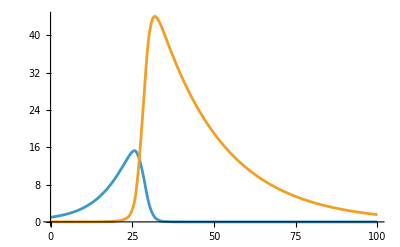

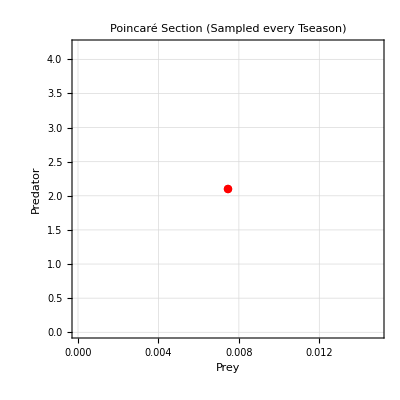

```mathematica
Plot[{preyFun[t],predFun[t]},{t,0,100}]
plotPoincareSection[params,100]
```

```mathematica
(*Sweep Tseason parameter and observe Poincaré sections*)TseasonSweep=Range[3,20,1];  (*You can fine-tune the range and step*)
tmax=500;  (*Simulation time*)

plots=
Table[
Module[
{newParams,poincare},
newParams=Association[params,"Tseason"->Tval];
poincare=plotPoincareSection[newParams,tmax];

Labeled[
poincare,"Tseason = "<>ToString[Tval],Top]],{Tval,TseasonSweep}];

(*Display in a grid*)
GraphicsGrid[Partition[plots,3],Spacings->{1,1}]
```

InterpolatingFunction::dmval: Input value {102} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {105} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {108} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## Parameter Sweep-Based Tests

### Amplitude Analysis

```mathematica
(*Amplitude Sweep:Aβ vs Prey Amplitude*)

amplitudeSweepData=Reap[
Do[
Module[
{paramsLocal,sol,preyFun,tmin=150,tmax=300,amp},
paramsLocal=params;
paramsLocal["Aβ"]=ab;
sol=Quiet@Check[simulateZombieSystem[paramsLocal],$Failed];

If[
ListQ[sol],preyFun=prey/. sol;
amp=MaxValue[{preyFun[t],tmin<=t<=tmax},t]-MinValue[{preyFun[t],tmin<=t<=tmax},t];

If[
NumericQ[amp],Sow[{ab,amp}]]]],{ab,0,1,0.05}]][[2,1]];

(*Plot the amplitude vs Aβ*)
ListLinePlot[amplitudeSweepData,Frame->True,FrameLabel->{"Aβ","Prey Amplitude (Max - Min)"},PlotStyle->Thick,PlotMarkers->Automatic,PlotRange->All,GridLines->Automatic]
```

InterpolatingFunction::dmval: Input value {156.86} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {150.031} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {150.088} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

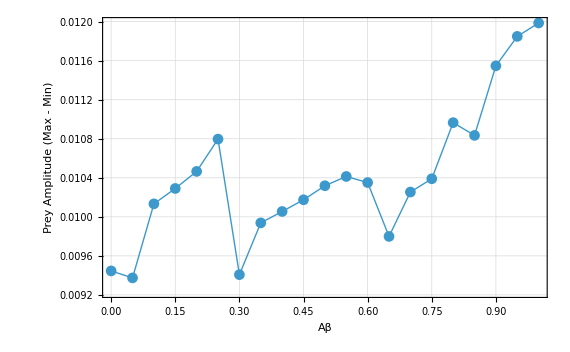

InterpolatingFunction::dmvali: The integration endpoint 150 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 200 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 150 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 200 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

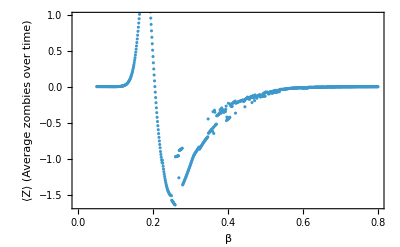

```mathematica
(*Example:average infected between t=150 and t=200*)

Zavg=NIntegrate[ZtotalFun[t],{t,150,200}]/50;
preyAvg=NIntegrate[preyFun[t],{t,150,200}]/50;
predAvg=NIntegrate[predFun[t],{t,150,200}]/50;

avgZdata=Reap[Do[Module[{paramsLocal,sol,Zfun,avgZ},
paramsLocal=params;
paramsLocal["beta"]=b;

sol=Quiet@Check[
simulateZombieSystem[paramsLocal],$Failed];

If[
ListQ[sol],
Z1f=Z1/. sol;
Z2f=Z2/. sol;
Z3f=Z3/. sol;
Zsum[t_]:=Z1f[t]+Z2f[t]+Z3f[t];
avgZ=Quiet@NIntegrate[Zsum[t],{t,150,200}]/50;

If[
NumericQ[avgZ],
Sow[{b,avgZ}]
]
]
]
,
{b,0.05,0.8,0.001}]][[2,1]];

(*Plot it*)
ListPlot[avgZdata,Frame->True,FrameLabel->{"β","⟨Z⟩ (Average zombies over time)"}]
```

### Ensemble simulation

```mathematica
(*---ENSEMBLE SIMULATIONS:Phase Portraits from Different Initial Conditions---*)
ClearAll[runEnsembleSimulations];

runEnsembleSimulations[baseParams_Association,preyRange_List,predatorRange_List,nSamples_:10,tmax_:100]:=
Module[
{results,preyFun,predFun,sols,trajs,colors},

(*Generate varied initial conditions*)
results=Table[
Module[
{params=baseParams,sol,prey0,pred0,solRules},
prey0=RandomReal[preyRange];
pred0=RandomReal[predatorRange];

(*Set new initial conditions*)
params["prey0"]=prey0;
params["predator0"]=pred0;
solRules=simulateZombieSystemWithInit[params];
preyFun=prey/. solRules;
predFun=predator/. solRules;

Table[
{preyFun[t],predFun[t]},
{t,0,tmax,0.5}]],
{nSamples}];

(*Plot all trajectories together*)
trajs=Map[ListLinePlot[#,PlotStyle->Opacity[0.4]]&,results];

Show[
trajs,
Frame->True,
FrameLabel->{"Prey","Predator"},
PlotLabel->"Ensemble Simulations with Varied Initial Conditions",
AspectRatio->1,
PlotRange->All
]
]

(*Helper version of simulateZombieSystem that takes varied prey0 and predator0*)
ClearAll[simulateZombieSystemWithInit];

simulateZombieSystemWithInit[params_Association]:=
Module[
{beta,gamma,a,b,c,d,interactionRate,kBeta,kGamma,Aβ,Aa,Tseason,phi,prey0,predator0,equations,solution,betaSeasonal,aSeasonal,betaEff,gammaEff,w1=1,w2=1.2,w3=0.8},

(*Extract parameters*)

beta=params["beta"];
gamma=params["gamma"];
a=params["a"];
b=params["b"];
c=params["c"];
d=params["d"];
interactionRate=params["interactionRate"];
kBeta=params["kBeta"];
kGamma=params["kGamma"];
Aβ=params["Aβ"];
Aa=params["Aa"];
Tseason=params["Tseason"];
phi=params["phi"];
prey0=Lookup[params,"prey0",0.99];
predator0=Lookup[params,"predator0",0.01];

(*Time-varying seasonal and coupling effects*)

betaSeasonal[t_]:=beta*(1+Aβ*Sin[2*Pi*t/Tseason]);
aSeasonal[t_]:=a*(1+Aa*Sin[2*Pi*t/Tseason+phi]);
betaEff[t_]:=betaSeasonal[t]/(1+kBeta*prey[t]);
gammaEff[t_]:=gamma*(1+kGamma*predator[t]/(1+predator[t]));
equations={
S'[t]==-betaEff[t] S[t] (w1 Z1[t]+w2 Z2[t]+w3 Z3[t]),
Z1'[t]==betaEff[t] w1 S[t] Z1[t]-gammaEff[t] Z1[t],
Z2'[t]==betaEff[t] w2 S[t] Z2[t]-gammaEff[t] Z2[t],
Z3'[t]==betaEff[t] w3 S[t] Z3[t]-gammaEff[t] Z3[t],
R'[t]==gammaEff[t] (Z1[t]+Z2[t]+Z3[t]),
prey'[t]==aSeasonal[t]*prey[t]-b*prey[t]*predator[t]-interactionRate*(Z1[t]+Z2[t]+Z3[t])*prey[t],
predator'[t]==c*prey[t]*predator[t]-d*predator[t],

(*Initial conditions*)
S[0]==0.99,
Z1[0]==0.005,
Z2[0]==0.003,
Z3[0]==0.002,
R[0]==0,
prey[0]==prey0,
predator[0]==predator0};

solution=NDSolve[
equations,
{S,Z1,Z2,Z3,R,prey,predator},
{t,0,100},
Method->"StiffnessSwitching"
];

First[solution]
]
```

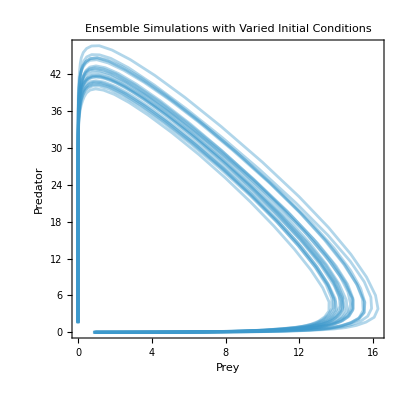

```mathematica
runEnsembleSimulations[params,{0.8,1.0},{0.005,0.02},20,100]
```